add the paclet to the path

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

import the code

```mathematica
<<Project`
```

do something with it

```mathematica
Binarize@ExampleData[{"TestImage","House"}]
```

-Graphics-

```mathematica
Hipsterize[ExampleData[{"TestImage","House"}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

use a function that was importing data locally

# Advanced Tests

## 1



```mathematica
image=Graphics[Disk[]]
```

```mathematica
Binarize@image
```

-Graphics-

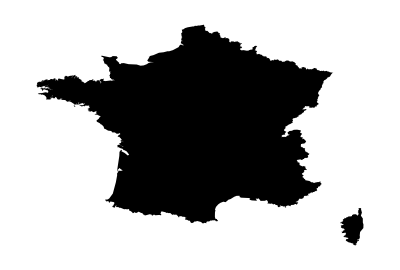

```mathematica
image =Graphics[LinguisticAssistant["Polygon"]]
```

```mathematica
newimage =ColorNegate@EdgeDetect[ImageResize[image,{80}]]
```

-Graphics-

```mathematica
Dimensions@ImageData@newimage
```

{55,80}

```mathematica
(*newimage=ColorNegate@(*Closing[#,DiskMatrix[5]]&@*)Thinning@ColorNegate@ImageResize[image,{75}]*)
matrix=ImageData[newimage];
Image@matrix
matrix=Replace[matrix, {0 -> 1, 1 -> 0}, Infinity];
```

-Graphics-

```mathematica
boundary=Thread[Position[matrix,1]->-1];
```

```mathematica
dim=Dimensions[matrix]
```

{55,80}

```mathematica
g=3/4;f=1/4;h=1/2;
Dimensions@RandomInteger[1,{Floor[dim[[1]]h]+1,Ceiling[dim[[2]]h]+1}]
```

{28,41}

```mathematica
mtest=SparseArray[{},{dim⟦1⟧,dim⟦2⟧}];Dimensions@mtest[[dim⟦1⟧-Floor[dim⟦1⟧g];;dim⟦1⟧-Floor[dim⟦1⟧f],dim[[2]]-Floor[dim[[2]]g];;dim[[2]]-Floor[dim[[2]]f]]]
```

{29,41}

```mathematica
mtest[[dim⟦1⟧-Floor[dim⟦1⟧g];;dim⟦1⟧-Floor[dim⟦1⟧f],dim[[2]]-Floor[dim[[2]]g];;dim[[2]]-Floor[dim[[2]]f]]]=RandomInteger[1,{Ceiling[dim[[1]]h]+1,Ceiling[dim[[2]]h]+1}];
ArrayPlot[mtest]
```

-Graphics-

```mathematica
randomImage[matrix_]:=Module[{m=matrix,neighbours},neighbours=ListConvolve[{{1,1,1},{1,0,1},{1,1,1}},ArrayPad[m,1]];
m=ReplacePart[m,Position[neighbours,_?(#<2||#>3&)]->0];
m=ReplacePart[m,Position[neighbours,3]->1];
m=ReplacePart[m,boundary]
]
```

```mathematica
limage=ArrayPlot[#,ColorRules->{1-> Black,0-> White,-1-> Red},ImageSize->Medium]&/@
NestList[randomImage,mtest,100];
```

```mathematica
Manipulate[limage[[n]],{n,4,100,1},ImageMargins->10,FrameMargins->10,ContentSize->Large,SaveDefinitions->True]
```

```mathematica
boundaryFunction[image_ImageQ]:=Module[{newimage =ColorNegate@EdgeDetect[ImageResize[image,{80}]],matrix=Null,boundary=Null},
matrix=ImageData[newimage];
matrix=Replace[matrix, {0 -> 1, 1 -> 0}, Infinity];
boundary=Thread[Position[matrix,1]->-1];
Return[boundary]]
```

## test for poster

```mathematica
image =Graphics[LinguisticAssistant["Polygon"]]
```